## Introduction

This document derives the matrix A in equation 18 of Blaser. For computational efficiency, this matrix is to be hard-coded in C, entry by entry. Furthermore, in the event that two or more of the axes lengths are the same, manual simplification is required in order to prevent divisions by 0. Let the axes lengths be denoted by a_1,a_2,a_3. The possible cases are:

a_1=a_2=a_3

a_1≠a_2, a_2=a_3

a_1=a_2, a_2≠a_3

a_1≠a_2≠a_3

Note that we ignore the case a_1=a_3, a_1≠a_2 because the axes lengths are always sorted in descending order. In this document we will derive explicit forms for each of the cases.

## Define Variables and Expressions

### Hard-Coded Quantities

These are the quantities we will take as input in the function computing A. Note that the indexing starts from 0. This is confusing since Mathematica indexes from 1 (and we must use this later), but if we don’t do it this way we are liable to code the results incorrectly in C, in which case we might find ourselves hunting a bug for weeks on end.  Because of the symmetry of the problem in our specific case (ellipsoid aligned with the axes, shear field is only nonzero for du/dy entry), we know that the rotation of the ellipsoid will be such that we can define the angular velocity and the velocity gradient in the ellipsoid frame in the manner below. See the notebook rotationR.nb for details.

```mathematica
asq={Subscript[a, 0]^2,Subscript[a, 1]^2,Subscript[a, 2]^2};
chi={Subscript[χ, 0],Subscript[χ, 1],Subscript[χ, 2]};
omega={0,0,ω};
G={{-Cos[θ]Sin[θ] γ,Cos[θ]^2 γ,0},{-Sin[θ]^2 γ, Cos[θ] Sin[θ] γ, 0},{0,0,0}};
```

### Intermediate Quantities

These quantities are used in the definition of A, but will not be computed in the final version as they are expressed in terms of the preceding variables.

```mathematica
ET=1/2 * (G+Transpose[G]);
ΩT=1/2 * (G-Transpose[G]);
AST[i_,j_,k_]:=LeviCivitaTensor[3][[i,j,k]];
sumfunction[i_,term_]:=Sum[Sum[AST[i,k,l]*(term[[k]]-term[[l]]),{l,1,3}],{k,1,3}];
chip[i_]:=FullSimplify[sumfunction[i,-chi]/sumfunction[i,asq]];
chipp[i_]:=FullSimplify[sumfunction[i,asq*chi]/sumfunction[i,asq]];
```

### The Matrix A

```mathematica
Adiagnum[i_]:=3*chipp[i]*ET[[i,i]]-Sum[chipp[l]*ET[[l,l]],{l,1,3}];
Adiagden[i_]:=6*(chipp[1]*chipp[2]+chipp[1]*chipp[3]+chipp[2]*chipp[3]);
Aoffdiagnum[k_,i_]:=chi[[i]]ET[[i,k]]+asq[[k]]*Sum[AST[i,k,l]*chip[l]*(AST[i,k,l]*ΩT[[k,i]]+omega[[l]]),{l,1,3}];
Aoffdiagden[k_,i_]:=2*(asq[[k]]*chi[[k]]+asq[[i]]*chi[[i]])*Sum[Abs[AST[i,k,l]]*chip[l],{l,1,3}];
```

## Indeterminate Forms

The elliptic integrals integrals χ_i are defined (equation 16) as 

χ_i=∫_0^∞ (t-a_i^2)^(-3/2)(t-a_j^2)^(-1/2)(t-a_k^2)^(-1/2)ⅆt

and so if a_i=a_j then χ_i=χ_j. This causes problems on the off-diagonal entries:

```mathematica
Table[
Table[
If[row==col,
"diag",
FullSimplify[Aoffdiagnum[row,col]/Aoffdiagden[row,col]]],
{col,3}],
{row,3}]//MatrixForm
```

(diag | ((γ-2 ω) a_0^2 (χ_0-χ_1)+γ Cos[2 θ] (-a_0^2+a_1^2) χ_1)/(4 (χ_0-χ_1) (a_0^2 χ_0+a_1^2 χ_1)) | 0
(γ Cos[2 θ] (-a_0^2+a_1^2) χ_0-(γ-2 ω) a_1^2 (χ_0-χ_1))/(4 (χ_0-χ_1) (a_0^2 χ_0+a_1^2 χ_1)) | diag | 0
0 | 0 | diag)

Looking at the numerator and denominator of a specific entry,

```mathematica
FullSimplify[Aoffdiagnum[1,2]]
FullSimplify[Aoffdiagden[1,2]]
```

1/2 (-((γ-2 ω) a_0^2 (χ_0-χ_1))/(a_0^2-a_1^2)+γ Cos[2 θ] χ_1)

(2 (-χ_0+χ_1) (a_0^2 χ_0+a_1^2 χ_1))/(a_0^2-a_1^2)

Both of these involve the fraction  (χ_1-χ_0)/(a_0^2-a_1^2) which evaluates to 0/0 when a_0=a_1. If we rearrange the full entry manually we can see the inverse of this fraction sitting in the second term below.

```mathematica
t1=FullSimplify[Aoffdiagnum[1,2][[1]] / Aoffdiagden[1,2]];
t2=FullSimplify[Aoffdiagnum[1,2][[2]] / Aoffdiagden[1,2]];
```

```mathematica
t1+t2
```

((γ-2 ω) a_0^2)/(4 (a_0^2 χ_0+a_1^2 χ_1))+(γ Cos[2 θ] (a_0^2-a_1^2) χ_1)/(4 (-χ_0+χ_1) (a_0^2 χ_0+a_1^2 χ_1))

To deal with this we re-express the fraction by combining the integrals:

χ_i-χ_j=(a_j^2-a_i^2)∫_0^∞ (t-a_i)^(-3/2)(t-a_j)^(-3/2)(t-a_k)^(-1/2)ⅆt

so that 

(χ_i-χ_j)/(a_i^2-a_j^2)=-∫_0^∞ (t-a_i)^(-3/2)(t-a_j)^(-3/2)(t-a_k)^(-1/2)ⅆt

which we can compute relatively efficiently. We name this quantity to simplify the expression of A. 

ξ_k:=(χ_i-χ_j)/(a_i^2-a_j^2)

```mathematica
s1=FullSimplify[Aoffdiagnum[2,1][[1]] / Aoffdiagden[2,1]];
s2=FullSimplify[Aoffdiagnum[2,1][[2]] / Aoffdiagden[2,1]];
```

```mathematica
s1+s2
```

-((γ-2 ω) a_1^2)/(4 (a_0^2 χ_0+a_1^2 χ_1))+(γ Cos[2 θ] (-a_0^2+a_1^2) χ_0)/(4 (χ_0-χ_1) (a_0^2 χ_0+a_1^2 χ_1))

```mathematica
FullSimplify[Adiagnum[1]]
FullSimplify[Adiagnum[2]]
FullSimplify[Adiagnum[3]]
```

γ Cos[θ] Sin[θ] ((-a_0^2 χ_0+a_2^2 χ_2)/(a_0^2-a_2^2)+(-2 a_1^2 χ_1+2 a_2^2 χ_2)/(a_1^2-a_2^2))

γ Cos[θ] Sin[θ] ((2 a_0^2 χ_0-2 a_2^2 χ_2)/(a_0^2-a_2^2)+(a_1^2 χ_1-a_2^2 χ_2)/(a_1^2-a_2^2))

γ Cos[θ] Sin[θ] ((a_1^2 χ_1-a_2^2 χ_2)/(a_1^2-a_2^2)+(-a_0^2 χ_0+a_2^2 χ_2)/(a_0^2-a_2^2))

```mathematica
Adiagden[1]
```

6 (((a_0^2 χ_0-a_1^2 χ_1) (a_0^2 χ_0-a_2^2 χ_2))/((a_0^2-a_1^2) (a_0^2-a_2^2))+((a_0^2 χ_0-a_1^2 χ_1) (a_1^2 χ_1-a_2^2 χ_2))/((a_0^2-a_1^2) (a_1^2-a_2^2))+((a_0^2 χ_0-a_2^2 χ_2) (a_1^2 χ_1-a_2^2 χ_2))/((a_0^2-a_2^2) (a_1^2-a_2^2)))

```mathematica
zfunc[k_]:={Subscript[a, 0]^2,Subscript[a, 1]^2,Subscript[a, 2]^2}[[k]]
χfunc[k_]:={Subscript[χ, 0],Subscript[χ, 1],Subscript[χ, 2]}[[k]]
βfunc[k_]:={(γ-2ω)/4,γ Cos[2θ]/4,γ Cos[θ]Sin[θ]/6}[[k]]
ξfunc[k_]:=(
{i,j}=Complement[{1,2,3},{k}];
(χfunc[i]-χfunc[j])/(zfunc[i]-zfunc[j])
)
ηfunc[k_]:=(
{i,j}=Complement[{1,2,3},{k}];
zfunc[i]*ξfunc[k]+χfunc[j]
)
```

```mathematica
s[k_]=k+1;
dd=ηfunc[s[2]]ηfunc[s[1]]+ηfunc[s[2]]ηfunc[s[0]]+ηfunc[s[1]]ηfunc[s[0]];
d0=βfunc[s[2]]*(-ηfunc[s[1]]-2ηfunc[s[0]])/dd;
d1=βfunc[s[2]]*(2*ηfunc[s[1]]+ηfunc[s[0]])/dd;
d2=-(d0+d1);
offdd=zfunc[s[0]]*χfunc[s[0]]+zfunc[s[1]]*χfunc[s[1]];
a01=(βfunc[s[0]]*zfunc[s[0]]-βfunc[s[1]]*(1/ξfunc[s[2]])*χfunc[s[1]])/offdd;
a10=(-βfunc[s[0]]*zfunc[s[1]]-βfunc[s[1]]*(1/ξfunc[s[2]])*χfunc[s[0]])/offdd;
newA={{d0,a01,0},{a10,d1,0},{0,0,d2}};
```

```mathematica
originalA = Table[
Table[
If[row==col,
Adiagnum[row]/Adiagden[row],
Aoffdiagnum[row,col]/Aoffdiagden[row,col]],
{col,3}],
{row,3}];
```

```mathematica
FullSimplify[newA-originalA]//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

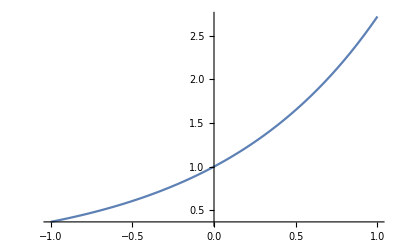

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Plot[Exp[x],{x,-1,1}]
```

```mathematica
pdfunscaled[x_,λ_]=Exp[-λ x];
const[λ_]=1/Sum[pdfunscaled[x,λ],{x,1,∞}];
cdf[xmin_,λ_]=Sum[const[λ]*pdfunscaled[x,λ],{x,1,xmin}];

xmin=5;
ϵ=0.01;
out=NSolve[cdf[λ,xmin]==1-ϵ,λ,Reals]
optfunc[λ,xmin]/.out
```

{}

(ⅇ^(-5 λ) (-1+ⅇ^(5 λ)))/((-1+ⅇ^λ)^2)

```mathematica
cdf[5,λ]
```

ⅇ^(-5 λ)/(-1+ⅇ^λ)+ⅇ^(-4 λ)/(-1+ⅇ^λ)+ⅇ^(-3 λ)/(-1+ⅇ^λ)+ⅇ^(-2 λ)/(-1+ⅇ^λ)+ⅇ^-λ/(-1+ⅇ^λ)

```mathematica
Sum[Exp[-λ x],{x,1,N}]
```

(ⅇ^(-N λ) (-1+ⅇ^(N λ)))/(-1+ⅇ^λ)

```mathematica
const[λ]
```

-1+ⅇ^λ

```mathematica
1/Sum[Exp[-λ x],{x,1,∞}]
```

-1+ⅇ^λ